```mathematica
SetDirectory[NotebookDirectory[]];
options3={Frame->{True,True,False,False},FrameStyle->Black,BaseStyle->{FontSize->20},LabelStyle->Black};
fNumericMean[aX_,α_,β_,y0_]:=Module[{y,x,f=NDSolveValue[{y'[x]==α y[x](1-β y[x]),y[0]==y0},y,{x,0,100}]},f[aX]]
fMean[x_,α_,β_,y0_]:=(ⅇ^(x α) y0)/(1-y0 β+ⅇ^(x α) y0 β)
fYGenerate[x_,α_,β_,y0_,σ_]:=RandomVariate[NormalDistribution[fMean[x,α,β,y0],σ],{1}][[1]]
fGenerateY[]:=Block[{lX =Table[x,{x,{1,1+2.7,1+2 2.7, 9.5}}],lY},lX=lX+RandomVariate[NormalDistribution[0,0.1],Length@lX];Thread[{lX,fYGenerate[#,0.5,0.05,5,3]&/@lX}]]
```

```mathematica
data=Table[fGenerateY[],{i,1,10,1}];
```

```mathematica
"BrightBands"
```

```mathematica
Needs["PolygonPlotMarkers`"]

allShapes=PolygonMarker[All];
Tooltip[Graphics[{FaceForm[Hue@Random[]],EdgeForm[{Black,Thickness[0.003],JoinForm["Miter"]}],PolygonMarker[#,1]},ImageSize->30,PlotRange->1.5,PlotRangePadding->0,ImagePadding->0],#]&/@allShapes;
allShapes = RandomSample[allShapes[[1;;30]]];
graphs=Graphics[{FaceForm[Blue],PolygonMarker[ToString@#,Scaled[0.04]]},AlignmentPoint->{0,0}]&/@allShapes[[3;;13]];
```

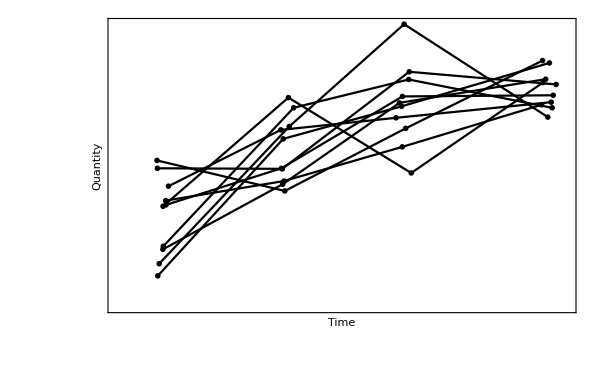
-Graphics-A. Time series

```mathematica
ga1=Labeled[ListLinePlot[data,PlotStyle->Black,PlotRange->{{0,10},Full},Joined->True,PlotMarkers ->graphs,ImageSize->600,FrameTicks->None,FrameStyle->Directive[Black,20,Thick],Frame->{True,True,False,False},FrameLabel->{"Time","Quantity"},ImagePadding->{{30,None},{30,None}}],"A. Time series", {{Top,Left}},LabelStyle->{Black,FontSize->20}]
```

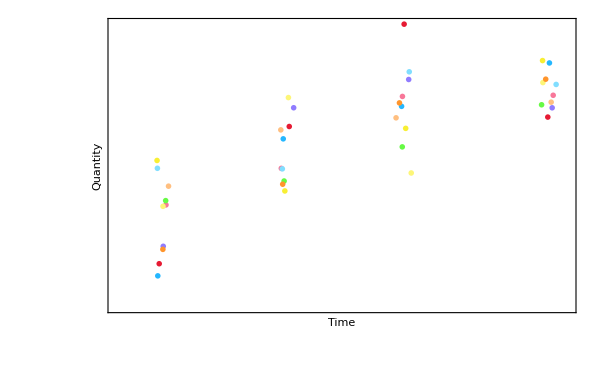
-Graphics-B. Snapshots

```mathematica
ga2=Labeled[ListPlot[data,PlotStyle->"BrightBands",PlotRange->{{0,10},Full},PlotMarkers ->Graphics[{FaceForm[Blue],PolygonMarker[ToString@"Disk",Scaled[0.04]]},AlignmentPoint->{0,0}],ImageSize->600,FrameTicks->None,FrameStyle->Directive[Black,20,Thick],Frame->{True,True,False,False},FrameLabel->{"Time","Quantity"},ImagePadding->{{30,None},{30,None}}],"B. Snapshots", {{Top,Left}},LabelStyle->{Black,FontSize->20}]
```

```mathematica
gFinal=GraphicsRow[{ga1,ga2},ImageSize->1300,Spacings->0]
```

-Graphics-

```mathematica
Export["../figures/time_series_v_snapshots.pdf",gFinal]
```

../figures/time_series_v_snapshots.pdf